## system A

```mathematica
θExactSystemA[θwplus1_,θwminus1_,τ_]:= Block[{deltaθ,θbar,f,y},

deltaθ = θwplus1-θwminus1;
θbar = (θwplus1+θwminus1)/2;

f[y_]:=(deltaθ y)/(2(1+τ))+θbar ;

f[y]

]
```

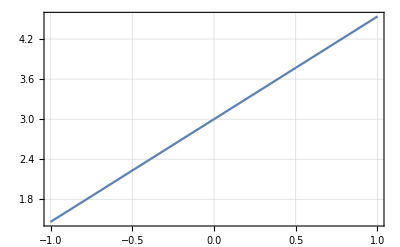

```mathematica
Plot[θExactSystemA[5,1,0.3],{y,-1,1},GridLines->Automatic,Frame->True]
```

```mathematica
trialexactθ[5,1,0.3]/.{y->-1}
```

1.46154